```mathematica
(* The Base directory when working on the lab computer *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research"}];
labComp=FileNameJoin[{"C:","Users","karl",dropBoxOn}];
homeComp=FileNameJoin[{"/","home","karl",dropBoxOn}];
(* Good graphing setup *)
labelSize=18;
(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{homeComp}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=1,i<=Length[directories],i++,
Print[i -> directories[[i]]];]
```

/home/karl/Dropbox/00School/research

1→3_15_17_AimingFor5e12

2→4-18-17

3→data

4→Data Before 4-1-17

5→firstRun2017

6→labBook

7→legacy

8→machineShopOrders

9→mathematicaCode

10→operationManuals

11→papers

12→polarization_4-18-17

13→polarization_4-4-17

14→polarization_4-6-17

15→probeLaserPower

16→pumpLaserFindingCircular_3-29_17

17→RbControlPiPrograms

18→rbsim

19→requisitions

20→wavemeterNoRb

21→wavemeterReliability_3-30-17

22→wmReliability_4-7-17

```mathematica
(* set rootFolder to the folder name containing the RbPolarization Files *)
rootFolder=FileNameJoin[{dataFolder,directories[[2]],"polarization","pol"}];
SetDirectory[rootFolder];
(* Obtain the filename of the absorption data *)
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
For[i=1,i<=Length[scanFiles],i++,
Print[i -> scanFiles[[i]]];]
```

1→FDayScan2017-04-18_164758RotationAnalysis.dat

2→FDayScan2017-04-18_165602RotationAnalysis.dat

3→FDayScan2017-04-18_170406RotationAnalysis.dat

4→FDayScan2017-04-18_171818RotationAnalysis.dat

5→FDayScan2017-04-18_172624RotationAnalysis.dat

6→FDayScan2017-04-18_173431RotationAnalysis.dat

```mathematica
modelA4=a1/(δ)^2+a2/(δ)^4+θ0;
modelA2=a1/(δ)^2+θ0;
modelB4=a1/(δ-b)^2+a2/(δ-b)^4+θ0;
modelB2=a1/(δ-b)^2+θ0;
ApproximateFrequency[data_,columnMissing_,columnReference_,missingEntry_]:=Module[{j,adjacentSpots,referenceSpacing,validEntries,fit},
validEntries=data[Select[#[[columnMissing]]>7000000&]];
referenceSpacing=data[[2]][[columnReference]]-data[[1]][[columnReference]];
j=1;
While[And[Length[adjacentSpots]<3,j*referenceSpacing<1024],
adjacentSpots=validEntries[Select[Abs[#[[columnReference]]-missingEntry]<=referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots],x,x];
fit[missingEntry]
];

FillInMissedFrequencies[data_,columnMissing_,columnReference_]:=Module[{referenceSpacing,missingEntries,validEntries,adjacentSpots,estimatedFrequency,linearModel,dataCopy,position,approxValue,data2,k},
data2=data;
dataCopy=Dataset[Take[data,{1,-1},{1,2}]];
missingEntries=dataCopy[Select[#[[columnMissing]]<7000000&]];
missingEntries=Transpose[Normal[missingEntries]][[columnReference]];
For[k=1,k<=Length[missingEntries],k++,
approxValue=ApproximateFrequency[dataCopy,columnMissing,columnReference,missingEntries[[k]]];
position=Position[dataCopy,missingEntries[[k]]][[1,1]];
data2[[position,columnMissing]]=approxValue;
];
data2
];

StripFaradayData[data_]:=Drop[Take[data,{rotAnalDataStartRow,-1},{aoutColumn,angleColumn}],None,{wavelengthColumn+1,angleColumn-wavelengthColumn+1}];

ConvertFDayWavelengthToDetune[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
wavelengthnm=wavelengthInteger/10000;
detuning=c/(wavelengthnm)-ν0;
Transpose[{detuning,θ}]
];

SetAsymptoteToZero[data_,nearResCutoff_,farResCutoff_]:=Module[{model,dataCopy,nlmFit,replacements},
dataCopy=Dataset[data];
dataCopy=dataCopy[Select[Abs[#[[1]]]>nearResCutoff&]];
dataCopy=dataCopy[Select[Abs[#[[1]]]<farResCutoff&]];
Print[dataCopy];
nlmFit =NonlinearModelFit[Normal[dataCopy],modelA4,{{a1,1},{a2,1},{θ0,33}},δ];
replacements=nlmFit["BestFitParameters"];

dataCopy=Transpose[Normal[dataCopy]];
dataCopy[[2]]=dataCopy[[2]]-θ0/.replacements;
Transpose[{dataCopy[[1]]-detuningOffset,dataCopy[[2]]}]
]
```

65.3

64.5

105.52-0.394071 x+0.759312 x^2

Transpose::nmtx: The first two levels of {} cannot be transposed.

{{29.0104,30.2693},{28.4411,30.5469},{27.255,30.543},{26.1638,30.5875},{25.2624,30.7007},{24.0763,30.7588},{22.7005,30.789},{21.4196,30.9962},{20.1387,30.998},{18.7629,31.2297},{17.3871,31.3855},{16.1062,31.5511},{14.683,31.5397},{13.2598,31.7914},{11.8366,32.1203},{10.4135,32.5498},{8.84798,33.1433},{7.47227,35.3435},{6.0017,27.5242},{4.43626,46.4307}}

Transpose::nmtx: The first two levels of {} cannot be transposed.

{{28.9155,32.898},{28.3936,33.2833},{27.3973,33.0605},{26.2587,33.2103},{25.12,33.4249},{23.9814,33.0347},{22.6056,32.8425},{21.3247,33.4018},{19.9963,33.1667},{18.7629,33.2279},{17.3396,33.6532},{15.9164,33.4699},{14.5407,33.3682},{13.07,33.6543},{11.5994,34.0414},{10.1763,34.5443},{8.70566,35.4593},{7.18764,40.7913},{5.76451,35.6312},{4.19908,55.4966}}

{{28.9155,29.184},{28.3936,29.0692},{27.255,28.9821},{26.0689,28.3707},{24.9303,29.7084},{23.7442,29.4405},{22.5107,29.1699},{21.1824,29.5237},{19.8184,30.388},{18.4782,30.1944},{17.1024,30.2214},{15.8216,30.078},{14.3984,30.1782},{13.0226,30.648},{11.5994,31.0578},{10.2237,31.6702},{8.70749,31.7782},{7.24238,34.4311},{5.76451,33.9112},{4.24651,52.3629}}

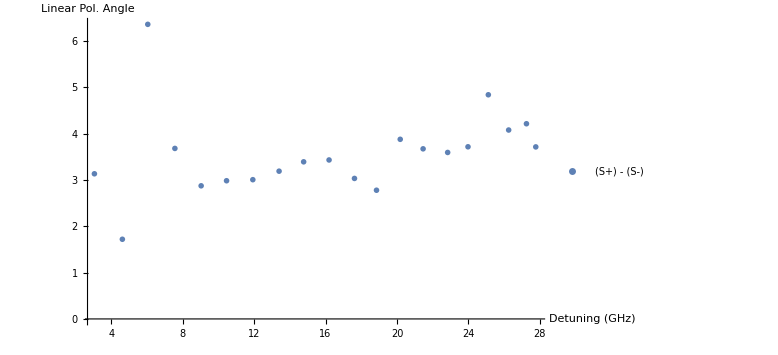

-Graphics-

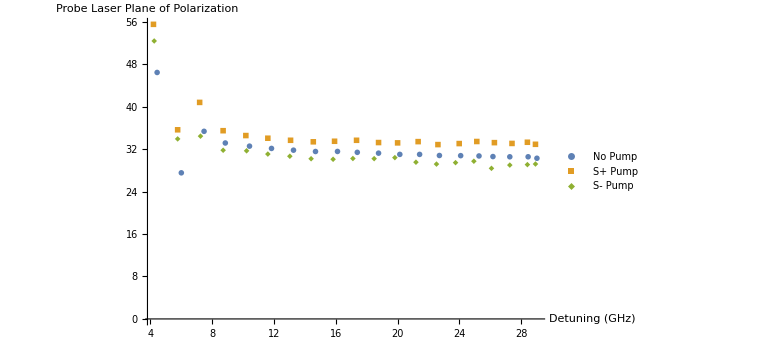

-Graphics-

```mathematica
(* Define important constants of data processing *)
firstFaradayFileNumber=1;
detuningOffset=1.144;
rotAnalDataStartRow=16;
wavelengthColumn=2;
angleColumn=10;

(* Define important physical constants*)
c=2.99792458*^8;
ν0=377107.463;
(* Retrieves the recorded voltages of the magnets *)
rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[firstFaradayFileNumber]]}],"tsv"];
v1=rotationAnalysisData[[11]][[2]]
v2=rotationAnalysisData[[12]][[2]]
(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1=v1*c1v2iSlope+c1v2iInt;
i2=v2*c2v2iSlope+c2v2iInt;

(*Creates a function for obtaining the magnetic field at a given position based on the currents
in the magnets *)
getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2)  ;
getBEq[i1,i2]
BdotL=Integrate[getBEq[i1,i2],{x,0,2.794}] /100/10000;(* Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)



rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[firstFaradayFileNumber]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
noPump=ConvertFDayWavelengthToDetune[rotationAnalysisData]


rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[firstFaradayFileNumber+1]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
sPlusPump=ConvertFDayWavelengthToDetune[rotationAnalysisData]


rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[firstFaradayFileNumber+2]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
sMinusPump=ConvertFDayWavelengthToDetune[rotationAnalysisData]


{detune,θm}=Transpose[sMinusPump];
{detune,θm}={detune,θm};
sMinusPump=Transpose[{detune,θm}];
{detune,θp}=Transpose[sPlusPump];
pumpDifference=Transpose[{detune-detuningOffset,θp-θm}];
differencePlot=ListPlot[Legended[pumpDifference,"(S+) - (S-)"],AxesLabel->{"Detuning (GHz)","Linear Pol. Angle"},PlotRange->All,LabelStyle->18,PlotMarkers->{Automatic,Large},ImageSize->Large]
Rasterize[differencePlot]
allPlot=ListPlot[{Legended[noPump,"No Pump"],Legended[sPlusPump,"S+ Pump"],Legended[sMinusPump,"S- Pump"]},PlotRange->All,LabelStyle->18,PlotMarkers->{Automatic,Large},ImageSize->Large,AxesLabel->{"Detuning (GHz)","Probe Laser\nPlane of Polarization"}]
Rasterize[allPlot]
```

FittedModel[4.55253-17.5608 x]

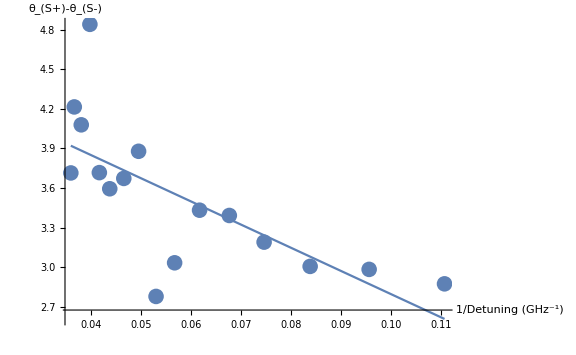

Integrated Magnetic Field (T*m):

0.000298806

Number Density (cm^-3):

1.3×10^14

Slope:

-17.5608

Polarization:

-0.00532158

Polarization Uncertainty:

0.00147649

```mathematica
(* Calculates fit for data *)
(* Removes datapoints that wrapped in rotation *)
lowerBoundDetuning=8;
upperBoundDetuning=30;

pumpDiff=Dataset[pumpDifference];
pumpDiff=pumpDiff[Select[Abs[#[[1]]]<upperBoundDetuning&]];
pumpDiff=pumpDiff[Select[Abs[#[[1]]]>lowerBoundDetuning&]];
pumpDiff=Normal[pumpDiff];
labelSize=18;

Clear[a,b,c,d,e]

(* Calculates fit for polarization *)
{detune,δθ}=Transpose[pumpDiff];
newThing=Transpose[{1/detune,δθ}];
lm=LinearModelFit[newThing,x,x]
polPlot=Plot[lm[x],{x,1/Min[detune],1/Max[detune]}];
Show[{ListPlot[newThing],polPlot},PlotRange->All,AxesLabel->{"1/Detuning\n(GHz^-1)","θ_(S+)-θ_(S-)"},LabelStyle->labelSize,ImageSize->Large]
slope=lm["BestFitParameters"][[2]];

Cpar=1.2692*^-11;
c=2.99792458*^8;
re=2.8179*^-15;
fge=0.34231;
k=4/3;
Print["Integrated Magnetic Field (T*m):"]
BdotL
μ=9.2740*^-24;
h=6.6261*^-34;
ν0=377107.463;
conversionFactor=h/(BdotL*c*re*fge*k*μ)*10^18*10^-6;(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)

Print["Number Density (cm^-3):"]
n=1.3*^14
Print["Slope:"];
Print[slope];
Print["Polarization:"]
pol=slope/(Cpar*n*2)
σSlope=lm["ParameterErrors"][[2]];
σDensity=1.055*^13;
Print["Polarization Uncertainty:"]
σp=Sqrt[pol^2*((σSlope/slope)^2+(σDensity/n)^2)]
```